```mathematica
Clear["Global`*"]
```

## Distributions for X=P(Y), finite Hill

### Distribution for Z=Y^n

Check normalisation

```mathematica
Pz[z_]:=PDF[NormalDistribution[μ,σ],z^(1/n)]/Abs[n*z^((n-1)/n)];
Pz2[z_]:=(PDF[NormalDistribution[μ,σ],z^(1/n)]+PDF[NormalDistribution[μ,σ],-z^(1/n)])/(n*z^((n-1)/n));
Integrate[Pz[z] /. {n->2},{z,-∞,∞}, Assumptions-> {z∈Reals,μ∈Reals, σ∈Reals, μ≥0,σ>0}]
```

Integrate::idiv: Integral of ⅇ^-(-√z + μ)^2/2\ σ^2/√Abs[z] does not converge on {-∞, ∞}.

Integrate[(ⅇ^(-(√z-μ)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[z]),{z,-∞,∞},Assumptions→{z∈Reals,μ∈Reals,σ∈Reals,μ≥0,σ>0}]

Separate into positive and negative parts

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x^(1/n)]*(n*x^((n-1)/n))^(-1) /. {n->2},{x,0,∞}, Assumptions-> {x∈Reals,μ∈Reals, σ∈Reals, μ≥0,σ>0}]
```

1/2 (1+Erf[μ/(√2 σ)])

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],-x^(1/n)]*(n*x^((n-1)/n))^(-1) /. {n->2},{x,0,∞}, Assumptions-> {n∈Integers,x∈Reals,μ∈Reals, σ∈Reals, μ≥0,σ>0}]
```

1/2 Erfc[μ/(√2 σ)]

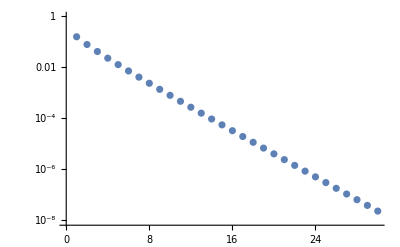

```mathematica
error = Table[N@(1/2) Erfc[μ/(√2 σ)]/.{μ->mu,σ->Sqrt[mu]},{mu,1,30}];
ListLogPlot[Transpose[{Range[1,30],error}]]
```

### Distribution for X(t+1) = (Y(t))^n/(K^n+(Y(t))^n)

NB μ, σ in this section are for Y, not for X.

From paper calculation
Probably wrong, not normalized

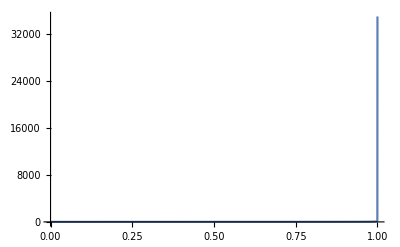

NIntegrate::inumr: The integrand Abs[k\ (x/1 - x)^1 - 1/n/n] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

NIntegrate[PQ[x],{x,0,1}]

```mathematica
Clear[μ,σ,n,k];params =  {k-> 10, n-> 2, μ-> 10,σ->2};PQ[u_]:= Abs[k/n(u/(1-u))^(1-1/n) ];PDF[NormalDistribution[μ,σ],(u/(1-u))^(1/n) k];

Plot[PQ[x] /. params,{x,0,1}, PlotRange-> All]
NIntegrate[PQ[x],{x,0,1}]
```

Check 1: brute force computing
Normalisation seems correct

```mathematica
Clear[μ,σ, μX,σX,fN, n,k];
Pz2[z_]:=(PDF[NormalDistribution[μ,σ],z^(1/n)]+PDF[NormalDistribution[μ,σ],-z^(1/n)])/(n*z^((n-1)/n));f[x_,y_]:= Pz2[x]*DiracDelta[x+k^n - y];
sol=Integrate[Abs[z] f[u z,z],{z,-∞,∞},
Assumptions-> {k^n∈Reals,k∈Reals,u ∈Reals, n∈Reals,x∈Reals,y∈Reals, k>0, n>0, μ>0, σ>0}]
```

(ⅇ^(-((k (-u/(-1+u))^(1/n)+μ)^2)/(2 σ^2)) (1+ⅇ^((2 k (-u/(-1+u))^(1/n) μ)/σ^2)) k (-u/(-1+u))^(-1+1/n))/(n √(2 π) (-1+u)^2 σ)

```mathematica
Simplify[-((k (-u/(-1+u))^(1/n)+μ)^2)/(2 σ^2)+(2 k (-u/(-1+u))^(1/n) μ)/σ^2]
```

-((-k (-u/(-1+u))^(1/n)+μ)^2)/(2 σ^2)

We see that the result is simply a Gaussian N(μ,σ), evaluated at k (u/(1-u))^(1/n). In addition, there is a normalisation term k/n (u/(1-u))^(-1+1/n)(1-u)^-2. Together this gives
P_(X(t+1))(u) = k/(n u(1-u)) (u/(1-u))^(1/n) N(μ,σ; k (u/(1-u))^(1/n))

```mathematica
Px[u_]:= k/(n u (1-u))(u/(1-u))^(1/n)PDF[NormalDistribution[μ,σ],(u/(1-u))^(1/n) k];
```

```mathematica
params =  {k->10, n-> 1, fN-> 2.5, Con->10, μX-> 0.5, σX-> 0.2};
moments = {μ -> μX+fN((Con-1)μX-1),
σ ->  Sqrt[fN^2(Con-1)^2+1]σX}  /. params;
NIntegrate[Px[u] /.moments/.params, {u,0,1}, AccuracyGoal->10]
```

0.979989

```mathematica
moments
```

{μ→9.25,σ→4.50444}

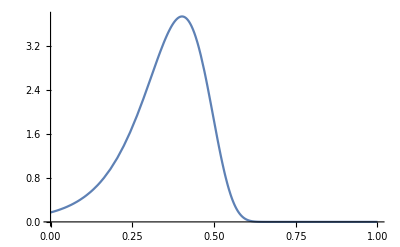

```mathematica
Plot[Px[u] /.moments /. params, {u,0,1}, PlotRange-> All]
```

Calculate new mean and standard deviation 
Only possible numerically

```mathematica
μnew = NIntegrate[u*Px[u] /.moments/. params,{u,0,1}];
x2new = NIntegrate[u^2*Px[u]/.moments /. params,{u,0,1}];
σnew = x2new - μnew^2;
Print["μ(t+1)=", μnew];
Print["σ(t+1)=", σnew];
```

μ(t+1)=0.450376

σ(t+1)=0.0202212

## μ_X(t), σ_X(t) trajectories

New step: compare calculated μ_X(t), σ_X(t) with simulations.
When distribution becomes too peaked, integrals diverge from the values they should give.

```mathematica
params =  {k->16, n-> 2, fN->3, Con->20};
μ0 =0.5; σ0=0.25; 
Px[u_]:= k/(n u (1-u))(u/(1-u))^(1/n)PDF[NormalDistribution[μ,σ],(u/(1-u))^(1/n) k];
f[μold_,σold_]:=Module[{x2new},
μY =(μold+fN)((Con-1)μold-1) /. params;
σY = Sqrt[fN^2(Con-1)^2+1]σold /. params;
μnew = NIntegrate[u*Px[u] /.{μ-> μY, σ-> σY} /. params,{u,0,1}, AccuracyGoal-> 20];
x2new = NIntegrate[u^2*Px[u] /.{μ-> μY, σ-> σY} /. params,{u,0,1},AccuracyGoal-> 20];
σnew = x2new - μnew^2;
{μnew, σnew}
];

Tsteps = 3;
trajectory = NestList[f[#[[1]], #[[2]]]&, {μ0,σ0}, Tsteps]
```

{{0.5,0.25},{0.694716,0.0533429},{0.886925,0.000189658},{0.,0.}}

Plot calculated distribution at time t

{μ→37.2935,σ→3.04101}

0.842438

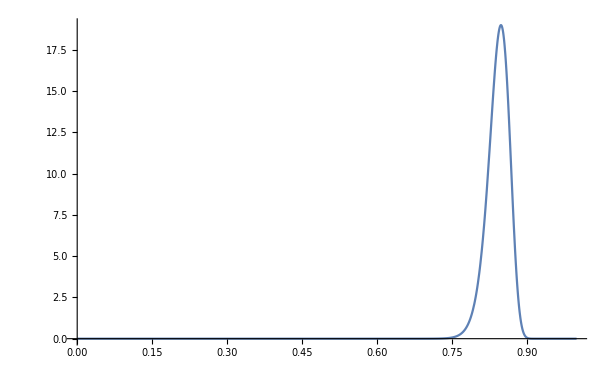

```mathematica
t=2;
moments = {μ -> μX+fN((Con-1)μX-1),
σ ->  Sqrt[fN^2(Con-1)^2+1]σX}  /. params /. {μX->trajectory[[t,1]], σX-> trajectory[[t,2]]}
NIntegrate[u Px[u] /.moments /. params,{u,0,1}, AccuracyGoal-> 100]
Plot[Px[u] /.moments /. params , {u,0,1},PlotRange-> All]
```

### Deterministic evolution

```mathematica
Needs["ErrorBarPlots`"];
```

Find first instance at which σ_X< ϵ and assume deterministic evolution afterwards.

```mathematica
ϵ=0.001; 
tdet=First@FirstPosition[trajectory[[;;,2]],n_/;n<ϵ];
x0 = trajectory[[tdet-1, 1]];
```

Solve deterministic equation for a further Tsteps

```mathematica
Tsteps=10;
params = {k->16, n-> 2, fN->3, Con->20};
fd[X_]:= Module[{Y}, 
Y=(1+fN)((Con-1)X-1); Y^n/(k^n+Y^n)/.params ];
xmean2=NestList[fd,x0, Tsteps];
```

Plot patched trajectory with error bars for the initial part with σ_X

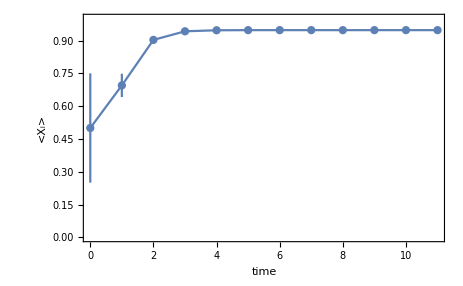

```mathematica
σvals = PadRight[ trajectory[[1;;tdet-1, 2]], Tsteps+tdet-1];
xmean = Join[trajectory[[1;;tdet-2,1]], xmean2];
p1=ErrorListPlot[Transpose[{Range[0,Tsteps+tdet-2],xmean,σvals}]];
p2=ListPlot[Transpose[{Range[0,Tsteps+tdet-2],xmean}], Joined-> True, PlotRange-> All];
fig=Show[p1,p2,PlotRange-> {Automatic,{0,1}}, AxesOrigin-> {0,0}, Frame-> True, FrameLabel-> {"time","<X_i>"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["trajectory_k16_Con20_fN3_hill2_ini_p0p5_sigma0p25.pdf", fig]
```

trajectory_k16_Con20_fN3_hill2_ini_p0p5_sigma0p25.pdf

## Single-cell dynamics

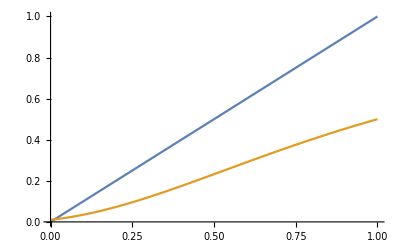

```mathematica
S[X_]:= 1+ (Con-1)*X;
fX[S_]:=S^n/(k^n+S^n);
Plot[{x,fX[S[x]] /. {k-> 10,Con-> 10, n-> 2}}, {x,0,1}]
```

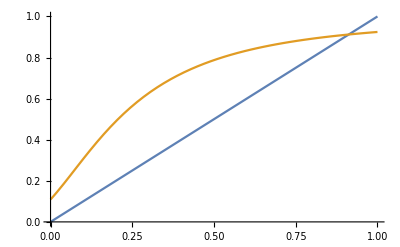

```mathematica
Plot[{x,fX[S[x]+fN*S[x] ] /. {k-> 10,Con-> 10, n-> 2, fN-> 2.5,xnei-> 0.5}}, {x,0,1}]
```

## Uniform lattice

Mathematica apparently cannot handle this complicated difference equation.

```mathematica
RSolve[{Xm[t+1] == ((1+fN)(Xm[t](Con-1)+1))^n/(((1+fN)(Xm[t](Con-1)+1))^n+k^n),Xm[0]==Xm0},Xm[t], t]
```

RSolve[{Xm[1+t]==((1+fN) (1+(-1+Con) Xm[t]))^n/(k^n+((1+fN) (1+(-1+Con) Xm[t]))^n),Xm[0]==Xm0},Xm[t],t]

```mathematica
RSolve[{Xm[t+1] == Xm[t]+1,Xm[0]==Xm0},Xm[t], t]
```

{{Xm[t]→t+Xm0}}